```mathematica
Name: Yue Sun            Student ID: 2880445            Email: sunyue@u.northwestern.edu             ME499  Project
```

## Project: Steel ball on a track Sine Waveform

```mathematica
Quit[];
```

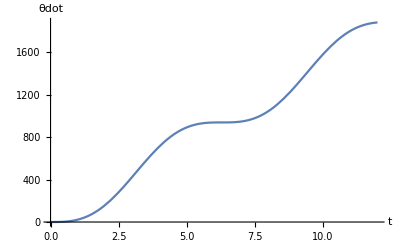

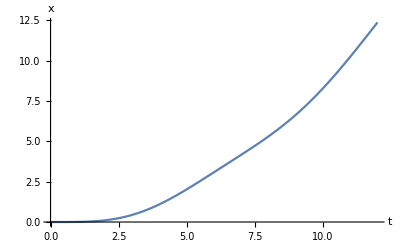

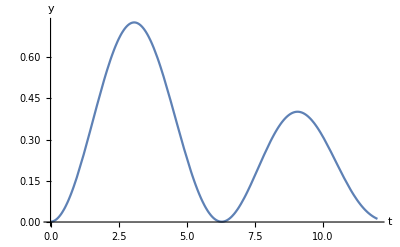

```mathematica
(*Define configuration variables as a column vector!!*)
q={{θ[t]}};
dq=D[q,t];
ddq=D[dq,t];

(*calculate by hand for ϕ[t]*)
velocity = 5*Sin[t]/200;
angle = 5*(1-Cos[t])/200;
(* make the angle to be +- 5 degree*)

R={{Cos[θ[t]],-Sin[θ[t]],0},{Sin[θ[t]],Cos[θ[t]],0},{0,0,1}};
p={{L-Cos[angle]*(L-θ[t]*r)+Sin[angle]*r},{Sin[angle]*(L-θ[t]*r)+Cos[angle]*r},{0}};
Rdot=D[R,t];
pdot=D[p,t];
V=Transpose[R].pdot;
W =Transpose[R].Rdot;
W3=W[[2,1]];
Vb={{V[[1,1]]},{V[[2,1]]},{V[[3,1]]},{0},{0},{W3}};
Inertia={{m,0,0,0,0,0},{0,m,0,0,0,0},{0,0,m,0,0,0},{0,0,0,2*m*r^2/5,0,0},{0,0,0,0,2*m*r^2/5,0},{0,0,0,0,0,2*m*r^2/5}};
KE=(1/2)*Transpose[Vb].Inertia.Vb;
KE=KE[[1,1]];
PE=m*g*Sin[angle]*(L-θ[t]*r)+Cos[angle]*r;
Lagrangian=KE-PE;
Eq=D[D[Lagrangian,θ'[t]],t]-D[Lagrangian,θ[t]]==0;
ELtemp=Solve[Eq,{θ''[t]}];
EL={θ''[t]==ELtemp[[1,1,2]]};

(*PARAMETERS*)
r=23/20000;   m=509/100000;   g=98/10;   L=15;  

(*Set Initial conditions in a list format because this is how NDSolve wants them!!*)
InitCon={θ'[0]==0, θ[0]==0};

(*Solve the equations of motion*)
sol=NDSolve[Join[EL,InitCon],{θ},{t,0,12}];
θsol=θ[t]/.sol[[1]];
θdotsol=θ'[t]/.sol[[1]];
xsol=L-Cos[5*(1-Cos[t])/200]*(L-θsol*r)+Sin[5*(1-Cos[t])/200]*r;
ysol=Sin[5*(1-Cos[t])/200]*(L-θsol*r)+Cos[5*(1-Cos[t])/200]*r;
Plot[θdotsol,{t,0,12}, AxesLabel->{t,θdot}]
Plot[xsol,{t,0,12}, AxesLabel->{t,x}]
Plot[ysol,{t,0,12}, AxesLabel->{t,y}]

X[τ_]:=xsol/.t-> τ;
Y[τ_]:=ysol/.t-> τ;
Animate[Show[Graphics[{PointSize[0.02],Point[{ X[τ],Y[τ]}],Line[{{L,0},{L*(1-Cos[5*(1-Cos[τ])/200]),L*Sin[5*(1-Cos[τ])/200]}}],Line[{{0,0},{15,0}}]}],PlotRange->{{0,15},{-1,1}}],{τ,0,12}]
```

## Project: Steel ball on a track Sine and -Sine Waveform

```mathematica
Quit[];
```

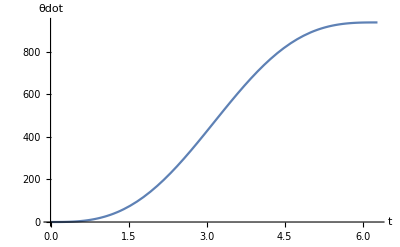

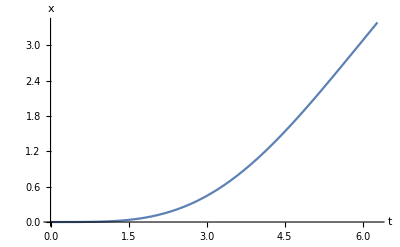

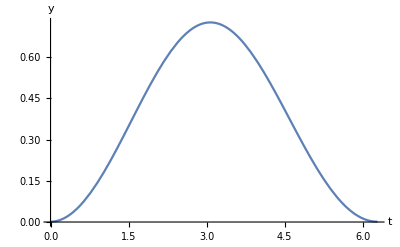

Piecewise[{{InterpolatingFunction[{{0., 6.28319}}, <>][t], 0<t<2 π}, {InterpolatingFunction[{{6.28319, 12.5664}}, <>][t], 2 π<t<4 π}, {0, True}}]

Piecewise[{{InterpolatingFunction[{{0., 6.28319}}, <>][t], 0<t<2 π}, {InterpolatingFunction[{{6.28319, 12.5664}}, <>][t], 2 π<t<4 π}, {0, True}}]

```mathematica
(*Define configuration variables as a column vector!!*)
q={{θ[t]}};
dq=D[q,t];
ddq=D[dq,t];

(*calculate by hand for ϕ[t]*)
velocity = 5*Sin[t]/200;
angle = 5*(1-Cos[t])/200;
(* make the angle to be +- 5 degree*)

R={{Cos[θ[t]],-Sin[θ[t]],0},{Sin[θ[t]],Cos[θ[t]],0},{0,0,1}};
p={{L-Cos[angle]*(L-θ[t]*r)+Sin[angle]*r},{Sin[angle]*(L-θ[t]*r)+Cos[angle]*r},{0}};
Rdot=D[R,t];
pdot=D[p,t];
V=Transpose[R].pdot;
W =Transpose[R].Rdot;
W3=W[[2,1]];
Vb={{V[[1,1]]},{V[[2,1]]},{V[[3,1]]},{0},{0},{W3}};
Inertia={{m,0,0,0,0,0},{0,m,0,0,0,0},{0,0,m,0,0,0},{0,0,0,2*m*r^2/5,0,0},{0,0,0,0,2*m*r^2/5,0},{0,0,0,0,0,2*m*r^2/5}};
KE=(1/2)*Transpose[Vb].Inertia.Vb;
KE=KE[[1,1]];
PE=m*g*Sin[angle]*(L-θ[t]*r)+Cos[angle]*r;
Lagrangian=KE-PE;
Eq=D[D[Lagrangian,θ'[t]],t]-D[Lagrangian,θ[t]]==0;
ELtemp=Solve[Eq,{θ''[t]}];
EL={θ''[t]==ELtemp[[1,1,2]]};

(*PARAMETERS*)
r=23/20000;   m=509/100000;   g=98/10;   L=15;  

(*Set Initial conditions in a list format because this is how NDSolve wants them!!*)
InitCon={θ'[0]==0, θ[0]==0};

(*Solve the equations of motion*)
sol1=NDSolve[Join[EL,InitCon],{θ},{t,0,2*Pi}];
θsol1=θ[t]/.sol1[[1]];
θdotsol1=θ'[t]/.sol1[[1]];
xsol1=L-Cos[5*(1-Cos[t])/200]*(L-θsol1*r)+Sin[5*(1-Cos[t])/200]*r;
ysol1=Sin[5*(1-Cos[t])/200]*(L-θsol1*r)+Cos[5*(1-Cos[t])/200]*r;
newθ=θ[2*Pi]/.sol1;
newθ=newθ[[1]];
newθdot=θ'[2*Pi]/.sol1;
newθdot=newθdot[[1]];
Plot[θdotsol1,{t,0,2*Pi}, AxesLabel->{t,θdot}]
Plot[xsol1,{t,0,2*Pi}, AxesLabel->{t,x}]
Plot[ysol1,{t,0,2*Pi}, AxesLabel->{t,y}]

(*calculate by hand for ϕ[t]*)
velocity2 = -5*Sin[t]/200;
angle2 = 5*(Cos[t]-1)/200;

R2={{Cos[θ[t]],-Sin[θ[t]],0},{Sin[θ[t]],Cos[θ[t]],0},{0,0,1}};
p2={{L-Cos[angle2]*(L-θ[t]*r)+Sin[angle2]*r},{Sin[angle2]*(L-θ[t]*r)+Cos[angle2]*r},{0}};
R2dot=D[R2,t];
p2dot=D[p2,t];
V2=Transpose[R2].p2dot;
W2 =Transpose[R2].R2dot;
W32=W2[[2,1]];
Vb2={{V2[[1,1]]},{V2[[2,1]]},{V2[[3,1]]},{0},{0},{W32}};
Inertia={{m,0,0,0,0,0},{0,m,0,0,0,0},{0,0,m,0,0,0},{0,0,0,2*m*r^2/5,0,0},{0,0,0,0,2*m*r^2/5,0},{0,0,0,0,0,2*m*r^2/5}};
KE2=(1/2)*Transpose[Vb2].Inertia.Vb2;
KE2=KE2[[1,1]];
PE2=m*g*Sin[angle2]*(L-θ[t]*r)+Cos[angle2]*r;
Lagrangian2=KE2-PE2;
Eq2=D[D[Lagrangian2,θ'[t]],t]-D[Lagrangian2,θ[t]]==0;
ELtemp2=Solve[Eq2,{θ''[t]}];
EL2={θ''[t]==ELtemp2[[1,1,2]]};

(*Set Initial conditions in a list format because this is how NDSolve wants them!!*)
InitCon2={θ'[2*Pi]==newθ, θ[2*Pi]==newθdot};
sol2=NDSolve[Join[EL2,InitCon2],{θ},{t,2*Pi,4*Pi}];

θvalue=Flatten[{{θ[t]/.sol1,0<t<2*Pi},{θ[t]/.sol2,2*Pi<t<4*Pi}}];
θdotvalue=Flatten[{{θ'[t]/.sol1,0<t<2*Pi},{θ'[t]/.sol2,2*Pi<t<4*Pi}}];

θθ=Piecewise[{{θvalue[[1]],θvalue[[2]]},{θvalue[[3]],θvalue[[4]]}}]
θθdot=Piecewise[{{θdotvalue[[1]],θdotvalue[[2]]},{θdotvalue[[3]],θdotvalue[[4]]}}]



(*X[τ_]:=xsol/.t-> τ;
Y[τ_]:=ysol/.t-> τ;
Animate[Show[Graphics[{PointSize[0.02],Point[{ X[τ],Y[τ]}],Line[{{L,0},{L*(1-Cos[5*(1-Cos[τ])/200]),L*Sin[5*(1-Cos[τ])/200]}}],Line[{{0,0},{15,0}}]}],PlotRange->{{0,15},{-1,1}}],{τ,0,10}]*)
```